```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
```

### New code: EDSLToTrana (only works for non-nested cases), AddLengthsToEDSL (better, still testing)

Function to calculate Repetitions & Lengths:

```mathematica
prepIC[x_]:=Replace[x,IndexedConcatenate[y__,iter_]:>ic[y,iterator[Sequence@@Flatten[{iter}]]],All]
```

```mathematica
unprepIC[x_]:=Replace[x,ic[y__,z_iterator]:>IndexedConcatenate[y,If[Length[z]==1,First[z],List@@z]],All]
```

```mathematica
RepsLen[l0_List] := Module[{l=prepIC[l0]},
If[FreeQ[l,List,{2,∞}],
If[$debug,Print[unprepIC[l],": ",{1,1}]];{1,1},
RepsLen /@ l]  (* non-nested list gets {1,1}, otherwise Thread it *)
];
(* CAUTION: use prepIC first, otherwise I-Cat iterators will be grabbed, too! *)

RepsLen[ic:ic[x__,iter_iterator]]:=Module[{argList={x},ans},
ans={ (* reps *)  If[Length[iter]==3,iter[[-1]]-iter[[-2]]+1,(* else *) Last@iter ],
(*  len  *) Dot@@Transpose[RepsLen /@ argList] (* multiply reps&len pairs, then add them up *)
};
If[$debug,Print[unprepIC[ic],": ",ans]];
ans
];
```

### Try it on ICN Paper Examples

### Figure 5a

```mathematica
IC2a={IndexedConcatenate[{1},10]}
```

{€^10[{1}]}

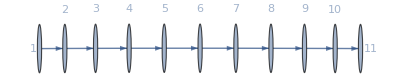

```mathematica
Graph[FromNetDifferenceSets[Expand[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

#### Testing RepsLen

```mathematica
RepsLen[IC2a]
```

```mathematica
{$debug=True,RepsLen[IC2a],$debug=False}[[2]]
```

{1}: {1,1}

€^10[{1}]: {10,1}

{{10,1}}

Perfect.

```mathematica
{{I-Cat, {, €^10[, {1}, ], }}, {reps(len), , 10(1)), , , }, {, , , 1(1), ↖, }}
```

### Figure 6d

```mathematica
IC3D1={IndexedConcatenate[IndexedConcatenate[IndexedConcatenate[{z=n(n+1)/2,z+i,z+i+1},i],{i,1,n}],{n,1,5}]}
```

{€_(n⊨1)^5[€_(i⊨1)^n[€^i[{1/2 n (1+n),i+1/2 n (1+n),1+i+1/2 n (1+n)}]]]}

```mathematica
{{I-Cat, {, €_(n⊨1)^5, €_(i⊨1)^n[, €^i[, {{z=1/2 n (1+n),i+z,1+i+z}, ], ], ], }}, {reps(len), , 5( i n), , , , , , , }, {, , , n(i), , , , , ↖, }, {, , , , i( 1), , , ↖, , }, {, , , , , 1(1), ↖, , , }}
```

```mathematica
Graph3D[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics3D-

```mathematica
{$debug=True,RepsLen[IC3D1],$debug=False}[[2]]
```

{1/2 n (1+n),i+1/2 n (1+n),1+i+1/2 n (1+n)}: {1,1}

€^i[{1/2 n (1+n),i+1/2 n (1+n),1+i+1/2 n (1+n)}]: {i,1}

€_(i⊨1)^n[€^i[{1/2 n (1+n),i+1/2 n (1+n),1+i+1/2 n (1+n)}]]: {n,i}

€_(n⊨1)^5[€_(i⊨1)^n[€^i[{1/2 n (1+n),i+1/2 n (1+n),1+i+1/2 n (1+n)}]]]: {5,i n}

{{5,i n}}

### Figure 5k

```mathematica
ICB5b={IndexedConcatenate[IndexedConcatenate[{1,12-2k},{k,1,4}],IndexedConcatenate[{1,1},{k,5,7}],{n,0,18}]}
```

{€_(n⊨0)^18[€_(k⊨1)^4[{1,12-2 k}],€_(k⊨5)^7[{1,1}]]}

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->None,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

```mathematica
{{I-Cat, {, □, □, □, □, □, □, □, □, □, □, □, □, ], }}, {reps(len), , (), , , , , , , , , , , , , }, {, , , (), (), , , , , , ( ), , , ( ), ↖, }, {, , , , , ()(), , , (), ↖, , ( ), ↖, , , }, {, , , , , , (), ↖, , , , , , , , }}
```

```mathematica
{$debug=True,RepsLen[ICB5b],$debug=False}[[2]]
```

{1,12-2 k}: {1,1}

€_(k⊨1)^4[{1,12-2 k}]: {4,1}

{1,1}: {1,1}

€_(k⊨5)^7[{1,1}]: {3,1}

€_(n⊨0)^18[€_(k⊨1)^4[{1,12-2 k}],€_(k⊨5)^7[{1,1}]]: {19,7}

{{19,7}}

### Figure 6a

```mathematica
IC2D1={IndexedConcatenate[{1,1,1},{1,1,1+i},IndexedConcatenate[{1,1,2+i},-1+i],{2+i,3+i},{i,1,10}]}
```

{€_(i⊨1)^10[{1,1,1},{1,1,1+i},€^(-1+i)[{1,1,2+i}],{2+i,3+i}]}

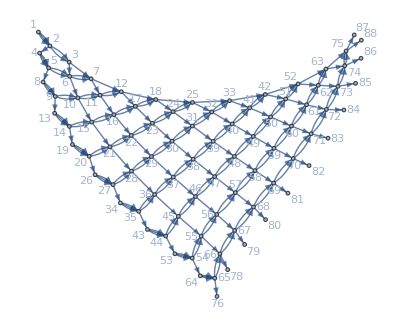

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
{{I-Cat, {, □, □, □, □, □, □, □, □, □, □, □, □, ], }}, {reps(len), , (), , , , , , , , , , , , , }, {, , , (), (), , , , , , ( ), , , ( ), ↖, }, {, , , , , ()(), , , (), ↖, , ( ), ↖, , , }, {, , , , , , (), ↖, , , , , , , , }}
```

```mathematica
{$debug=True,RepsLen[IC2D1],$debug=False}[[2]]
```

{1,1,1}: {1,1}

{1,1,1+i}: {1,1}

{1,1,2+i}: {1,1}

€^(-1+i)[{1,1,2+i}]: {-1+i,1}

{2+i,3+i}: {1,1}

€_(i⊨1)^10[{1,1,1},{1,1,1+i},€^(-1+i)[{1,1,2+i}],{2+i,3+i}]: {10,2+i}

{{10,2+i}}

### Figure 5b

```mathematica
IC2b={IndexedConcatenate[{1},{},{n,1,5}]}
```

{€_(n⊨1)^5[{1},{}]}

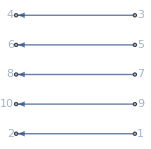

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
{$debug=True,RepsLen[IC2b],$debug=False}[[2]]
```

{1}: {1,1}

{}: {1,1}

€_(n⊨1)^5[{1},{}]: {5,2}

{{5,2}}

### Figure 5c

```mathematica
IC2c={IndexedConcatenate[{1,2},{n,1,10}]}
```

{€_(n⊨1)^10[{1,2}]}

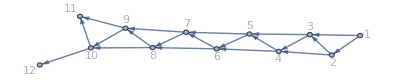

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
{{I-Cat, {, □, □, □, □, □, □, □, □, □, □, □, □, ], }}, {reps(len), , (), , , , , , , , , , , , , }, {, , , (), (), , , , , , ( ), , , ( ), ↖, }, {, , , , , ()(), , , (), ↖, , ( ), ↖, , , }, {, , , , , , (), ↖, , , , , , , , }}
```

```mathematica
{$debug=True,RepsLen[IC2c],$debug=False}[[2]]
```

{1,2}: {1,1}

€_(n⊨1)^10[{1,2}]: {10,1}

{{10,1}}

### Figure 6d

```mathematica
IC2d={IndexedConcatenate[{2,3},{3},{1,2},{m,1,9}]}
```

{€_(m⊨1)^9[{2,3},{3},{1,2}]}

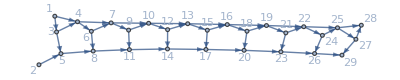

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
{{I-Cat, {, □, □, □, □, □, □, □, □, □, □, □, □, ], }}, {reps(len), , (), , , , , , , , , , , , , }, {, , , (), (), , , , , , ( ), , , ( ), ↖, }, {, , , , , ()(), , , (), ↖, , ( ), ↖, , , }, {, , , , , , (), ↖, , , , , , , , }}
```

```mathematica
{$debug=True,RepsLen[IC2d],$debug=False}[[2]]
```

{2,3}: {1,1}

{3}: {1,1}

{1,2}: {1,1}

€_(m⊨1)^9[{2,3},{3},{1,2}]: {9,3}

{{9,3}}

### Figure 5e

EDSL representations:

```mathematica
ICNB11={IndexedConcatenate[IndexedConcatenate[{2j-1, 2j}, {j, 1, 3}], IndexedConcatenate[{1, 2}, IndexedConcatenate[{}, 2], 2], 3]};
ICNB10={IndexedConcatenate[IndexedConcatenate[{2j+1, 2j+2}, {j,0,2}], IndexedConcatenate[{1, 2}, IndexedConcatenate[{}, {k,0,1}],{j,0,1}],{i,0,2}]};
Grid[{{ICNB11,Column[Partition[Expand[ICNB11],9]]},{ICNB10,SpanFromAbove}},Spacings->2,Alignment->{{Left,Left},{Center}}]
```

{€^3[€_(j⊨1)^3[{-1+2 j,2 j}],€^2[{1,2},€^2[{}]]]} | {{1,2},{3,4},{5,6},{1,2},{},{},{1,2},{},{}}
{{1,2},{3,4},{5,6},{1,2},{},{},{1,2},{},{}}
{{1,2},{3,4},{5,6},{1,2},{},{},{1,2},{},{}}
{€_(i⊨0)^2[€_(j⊨0)^2[{1+2 j,2+2 j}],€_(j⊨0)^1[{1,2},€_(k⊨0)^1[{}]]]} |

```mathematica
{{I-Cat, {, □, □, □, □, □, □, □, □, □, □, □, □, ], }}, {reps(len), , (), , , , , , , , , , , , , }, {, , , (), (), , , , , , ( ), , , ( ), ↖, }, {, , , , , ()(), , , (), ↖, , ( ), ↖, , , }, {, , , , , , (), ↖, , , , , , , , }}
```

```mathematica
{$debug=True,RepsLen[ICNB11],$debug=False}[[2]]
```

{-1+2 j,2 j}: {1,1}

€_(j⊨1)^3[{-1+2 j,2 j}]: {3,1}

{1,2}: {1,1}

{}: {1,1}

€^2[{}]: {2,1}

€^2[{1,2},€^2[{}]]: {2,3}

€^3[€_(j⊨1)^3[{-1+2 j,2 j}],€^2[{1,2},€^2[{}]]]: {3,9}

{{3,9}}

#### Musings

There are 9 edge difference sets in each row of the EDSL — for each “i” in the outer I-Cat, but they describe 10 edges, given below:

```mathematica
Grid[Riffle[#,","]& /@ Partition[FromNetDifferenceSets[ExpandAll[ICNB11]],10]]
```

1→2 | , | 1→3 | , | 2→5 | , | 2→6 | , | 3→8 | , | 3→9 | , | 4→5 | , | 4→6 | , | 7→8 | , | 7→9
10→11 | , | 10→12 | , | 11→14 | , | 11→15 | , | 12→17 | , | 12→18 | , | 13→14 | , | 13→15 | , | 16→17 | , | 16→18
19→20 | , | 19→21 | , | 20→23 | , | 20→24 | , | 21→26 | , | 21→27 | , | 22→23 | , | 22→24 | , | 25→26 | , | 25→27

The lengths of the internal ICs are 3×1=3, 2×(1+2×1)=6 , and 2×1=2.  The 9 comes from adding up the lengths of the ICs at the second level, that is, 3×1 + 2×(1+2×1)=3+2×3=3+6=9 elements

There is only 1 edge difference set inside the first “j” I-Cat, and 3 inside the second. In the following, 
(9i+j) comes from the 9 EDSs in the outer I-Cat and the 1 in the first “j” I-Cat;
(9i+3+3j) ”      ”        ”   9 EDSs  ”     ”       ”          ” ,   the 3 in order to to pass the first “j” I-Cat entirely, the 3j comes from the 3 EDSs in the 2nd “j” I-Cat. 
The final integer before each “→” is the vertex number in the inner I-Cat: 1.
The parenthesized expressions at the end of each “→” expression come from the EDSL internal expressions, when 0-indexed (2nd form shown above).

```mathematica
ICNB1TranaTemp=
{IndexedConcatenate[
IndexedConcatenate[Association[vertex->(9i+j)+1,EDS->{2 j+1,2 j+2}],{j,0,2}],
IndexedConcatenate[Association[vertex->(9i+3+3j)+1,EDS->{1,2}],{j,0,1}],
{i,0,2}
]}
```

```mathematica
ICNB1Trana=
{IndexedConcatenate[
IndexedConcatenate[(9i+j)+1->(9i+j)+1+(2j+1),(9i+j)+1->(9i+j)+1+(2j+2),{j,0,2}],
IndexedConcatenate[(9i+3+3j)+1->(9i+3+3j)+1+(1),(9i+3+3j)+1->(9i+3+3j)+1+(2),{j,0,1}],
{i,0,2}
]}
```

{€_(i⊨0)^2[€_(j⊨0)^2[1+9 i+j→2+9 i+3 j,1+9 i+j→3+9 i+3 j],€_(j⊨0)^1[4+9 i+3 j→5+9 i+3 j,4+9 i+3 j→6+9 i+3 j]]}

{€_(i⊨0)^2[€_(j⊨0)^2[(9i+j)+1->(9i+j)+1+(2j+1),(9i+j)+1->(9i+j)+1+(2j+2),],€_(j⊨0)^1[(9i+3+3j)+1->(9i+3+3j)+1+(1),(9i+3+3j)+1->(9i+3+3j)+1+(2)]]}

```mathematica
ExpandAll[ICNB1Trana]
```

{1→2,1→3,2→5,2→6,3→8,3→9,4→5,4→6,7→8,7→9,10→11,10→12,11→14,11→15,12→17,12→18,13→14,13→15,16→17,16→18,19→20,19→21,20→23,20→24,21→26,21→27,22→23,22→24,25→26,25→27}

```mathematica
FromNetDifferenceSets@ExpandAll[ICNB11]
```

{1→2,1→3,2→5,2→6,3→8,3→9,4→5,4→6,7→8,7→9,10→11,10→12,11→14,11→15,12→17,12→18,13→14,13→15,16→17,16→18,19→20,19→21,20→23,20→24,21→26,21→27,22→23,22→24,25→26,25→27}

```mathematica
%133==%134
```

True

```mathematica
Expand[%]
```

```mathematica
Graph[%,VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

What we need is  the # reps (number of repetitions) and length (of the argument list for each Indexed Concatenation object.  Suppose for convenience we put the nested ICat in a table (using Insert => Table):

□ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □

Then we copy the various parts in, leaving room for the reps & length information, using Ctrl-, to add more columns, if needed. (DEL deletes rows or columns):

I-Cat: | { | €_(i⊨0)^2[ | €_(j⊨0)^2[ | {2 j+1,2 j+2} | ] | , | €_(j⊨0)^1[ | {1,2} | , | €_(k⊨0)^1[ | {} | ] | ] | }
reps: | / | 3 | 3 | 1 | / | / | 2 | 1 | / | 2 | 1 | / | / | /
length: | / | □ | □ | 1 | □ | □ | □ | 1 | / | □ | 1 | / | / | /

Parts filled in from:

{€_(i⊨0)^2[€_(j⊨0)^2[{2 j+1,2 j+2}],€_(j⊨0)^1[{1,2},€_(k⊨0)^1[{}]]]}

All sets of integers count as reps = 1, length = 1.  (length > 1 would include multiple sets inside the I-Cat brackets.)

Now we start to work from the inside out to find the lengths of the I-Cats themselves.  If the contents is fixed, that’s just adding up the reps × length of what’s inside:

I-Cat: | { | €_(i⊨0)^2[ | €_(j⊨0)^2[ | {2 j+1,2 j+2} | ] | , | €_(j⊨0)^1[ | {1,2} | , | €_(k⊨0)^1[ | {} | ] | ] | }
reps: | / | 3 | 3 | 1 | / | / | 2 | 1 | / | 2 | 1 | / | / | /
length: | / | 9=(3×1)+(2×3) | 1 | 1 | / | / | 3=(1×1)+(2×1) | 1 | / | 1=(1×1) | 1 | / | / | /

So we get the reps & length for the 4 ICats above: {3,9}, {3,1}, {2,3}, and {2,1} respectively.

### Figure 5f

```mathematica
ICNB2={IndexedConcatenate[{2,2,2},{1,3,3},{2},{1,1,3},{2},{1,1,1},{3},4]}
```

{€^4[{2,2,2},{1,3,3},{2},{1,1,3},{2},{1,1,1},{3}]}

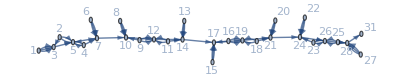

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
{{I-Cat, {, □, □, □, □, □, □, □, □, □, □, □, □, ], }}, {reps(len), , (), , , , , , , , , , , , , }, {, , , (), (), , , , , , ( ), , , ( ), ↖, }, {, , , , , ()(), , , (), ↖, , ( ), ↖, , , }, {, , , , , , (), ↖, , , , , , , , }}
```

```mathematica
{$debug=True,RepsLen[ICNB2],$debug=False}[[2]]
```

{2,2,2}: {1,1}

{1,3,3}: {1,1}

{2}: {1,1}

{1,1,3}: {1,1}

{2}: {1,1}

{1,1,1}: {1,1}

{3}: {1,1}

€^4[{2,2,2},{1,3,3},{2},{1,1,3},{2},{1,1,1},{3}]: {4,7}

{{4,7}}

### Figure 5g

```mathematica
ICNB3={IndexedConcatenate[{2, 3}, {1, 2}, {}, 8]}
```

{€^8[{2,3},{1,2},{}]}

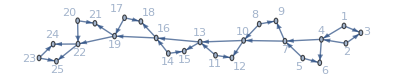

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
{{I-Cat, {, □, □, □, □, □, □, □, □, □, □, □, □, ], }}, {reps(len), , (), , , , , , , , , , , , , }, {, , , (), (), , , , , , ( ), , , ( ), ↖, }, {, , , , , ()(), , , (), ↖, , ( ), ↖, , , }, {, , , , , , (), ↖, , , , , , , , }}
```

```mathematica
{$debug=True,RepsLen[ICNB3],$debug=False}[[2]]
```

{2,3}: {1,1}

{1,2}: {1,1}

{}: {1,1}

€^8[{2,3},{1,2},{}]: {8,3}

{{8,3}}

### Figure 5h

```mathematica
ICNB4={IndexedConcatenate[{1, 6, 8}, {}, {IndexedConcatenate[2,4]}, IndexedConcatenate[{1, IndexedConcatenate[3,3]}, {}, 2], 7]}
```

{€^7[{1,6,8},{},{€^4[2]},€^2[{1,€^3[3]},{}]]}

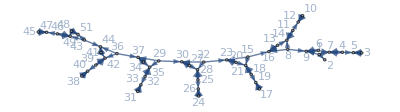

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
{{I-Cat, {, □, □, □, □, □, □, □, □, □, □, □, □, ], }}, {reps(len), , (), , , , , , , , , , , , , }, {, , , (), (), , , , , , ( ), , , ( ), ↖, }, {, , , , , ()(), , , (), ↖, , ( ), ↖, , , }, {, , , , , , (), ↖, , , , , , , , }}
```

```mathematica
{$debug=True,RepsLen[ICNB4],$debug=False}[[2]]
```

{1,6,8}: {1,1}

{}: {1,1}

{€^4[2]}: {1,1}

{1,€^3[3]}: {1,1}

{}: {1,1}

€^2[{1,€^3[3]},{}]: {2,2}

€^7[{1,6,8},{},{€^4[2]},€^2[{1,€^3[3]},{}]]: {7,7}

{{7,7}}

### Figure 5i

```mathematica
ICB5={IndexedConcatenate[IndexedConcatenate[{1,18-2k},{k,1,7}],IndexedConcatenate[{1,1},{k,8,9}],{n,0,25}]}
```

{€_(n⊨0)^25[€_(k⊨1)^7[{1,18-2 k}],€_(k⊨8)^9[{1,1}]]}

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->None,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

```mathematica
{{I-Cat, {, □, □, □, □, □, □, □, □, □, □, □, □, ], }}, {reps(len), , (), , , , , , , , , , , , , }, {, , , (), (), , , , , , ( ), , , ( ), ↖, }, {, , , , , ()(), , , (), ↖, , ( ), ↖, , , }, {, , , , , , (), ↖, , , , , , , , }}
```

```mathematica
{$debug=True,RepsLen[ICB5],$debug=False}[[2]]
```

{1,18-2 k}: {1,1}

€_(k⊨1)^7[{1,18-2 k}]: {7,1}

{1,1}: {1,1}

€_(k⊨8)^9[{1,1}]: {2,1}

€_(n⊨0)^25[€_(k⊨1)^7[{1,18-2 k}],€_(k⊨8)^9[{1,1}]]: {26,9}

{{26,9}}

### Figure 5j

```mathematica
ICB6={IndexedConcatenate[IndexedConcatenate[{1,7,8},2],IndexedConcatenate[{1,1,7},2],{7},{},{},13]}
```

{€^13[€^2[{1,7,8}],€^2[{1,1,7}],{7},{},{}]}

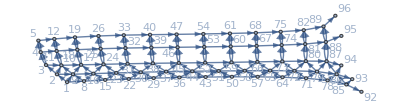

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
{{I-Cat, {, □, □, □, □, □, □, □, □, □, □, □, □, ], }}, {reps(len), , (), , , , , , , , , , , , , }, {, , , (), (), , , , , , ( ), , , ( ), ↖, }, {, , , , , ()(), , , (), ↖, , ( ), ↖, , , }, {, , , , , , (), ↖, , , , , , , , }}
```

```mathematica
{$debug=True,RepsLen[ICB6],$debug=False}[[2]]
```

{1,7,8}: {1,1}

€^2[{1,7,8}]: {2,1}

{1,1,7}: {1,1}

€^2[{1,1,7}]: {2,1}

{7}: {1,1}

{}: {1,1}

{}: {1,1}

€^13[€^2[{1,7,8}],€^2[{1,1,7}],{7},{},{}]: {13,7}

{{13,7}}

### Figure 5k

```mathematica
ICB5b={IndexedConcatenate[IndexedConcatenate[{1,12-2k},{k,1,4}],IndexedConcatenate[{1,1},{k,5,7}],{n,0,18}]}
```

{€_(n⊨0)^18[€_(k⊨1)^4[{1,12-2 k}],€_(k⊨5)^7[{1,1}]]}

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->None,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

```mathematica
{{I-Cat, {, □, □, □, □, □, □, □, □, □, □, □, □, ], }}, {reps(len), , (), , , , , , , , , , , , , }, {, , , (), (), , , , , , ( ), , , ( ), ↖, }, {, , , , , ()(), , , (), ↖, , ( ), ↖, , , }, {, , , , , , (), ↖, , , , , , , , }}
```

```mathematica
{$debug=True,RepsLen[ICB5b],$debug=False}[[2]]
```

{1,12-2 k}: {1,1}

€_(k⊨1)^4[{1,12-2 k}]: {4,1}

{1,1}: {1,1}

€_(k⊨5)^7[{1,1}]: {3,1}

€_(n⊨0)^18[€_(k⊨1)^4[{1,12-2 k}],€_(k⊨5)^7[{1,1}]]: {19,7}

{{19,7}}

### Figure 6a

```mathematica
IC2D1={IndexedConcatenate[{1,1,1},{1,1,1+i},IndexedConcatenate[{1,1,2+i},-1+i],{2+i,3+i},{i,1,10}]}
```

{€_(i⊨1)^10[{1,1,1},{1,1,1+i},€^(-1+i)[{1,1,2+i}],{2+i,3+i}]}

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

```mathematica
{{I-Cat, {, □, □, □, □, □, □, □, □, □, □, □, □, ], }}, {reps(len), , (), , , , , , , , , , , , , }, {, , , (), (), , , , , , ( ), , , ( ), ↖, }, {, , , , , ()(), , , (), ↖, , ( ), ↖, , , }, {, , , , , , (), ↖, , , , , , , , }}
```

```mathematica
{$debug=True,RepsLen[IC2D1],$debug=False}[[2]]
```

{1,1,1}: {1,1}

{1,1,1+i}: {1,1}

{1,1,2+i}: {1,1}

€^(-1+i)[{1,1,2+i}]: {-1+i,1}

{2+i,3+i}: {1,1}

€_(i⊨1)^10[{1,1,1},{1,1,1+i},€^(-1+i)[{1,1,2+i}],{2+i,3+i}]: {10,2+i}

{{10,2+i}}

### Figure 6b

```mathematica
IC2D2={IndexedConcatenate[{-1+2 k,1+2 k},IndexedConcatenate[{1,1},{1,2 k},k],{k,1,12}]}
```

{€_(k⊨1)^12[{-1+2 k,1+2 k},€^k[{1,1},{1,2 k}]]}

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->None,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

```mathematica
{{I-Cat, {, □, □, □, □, □, □, □, □, □, □, □, □, ], }}, {reps(len), , (), , , , , , , , , , , , , }, {, , , (), (), , , , , , ( ), , , ( ), ↖, }, {, , , , , ()(), , , (), ↖, , ( ), ↖, , , }, {, , , , , , (), ↖, , , , , , , , }}
```

```mathematica
{$debug=True,RepsLen[IC2D2],$debug=False}[[2]]
```

{-1+2 k,1+2 k}: {1,1}

{1,1}: {1,1}

{1,2 k}: {1,1}

€^k[{1,1},{1,2 k}]: {k,2}

€_(k⊨1)^12[{-1+2 k,1+2 k},€^k[{1,1},{1,2 k}]]: {12,1+2 k}

{{12,1+2 k}}

### Figure 6c

```mathematica
IC2D4={IndexedConcatenate[IndexedConcatenate[{},{1,1,2,2k},k-1],{},{2k,2(1+k)},{k,1,8}]}
```

{€_(k⊨1)^8[€^(-1+k)[{},{1,1,2,2 k}],{},{2 k,2 (1+k)}]}

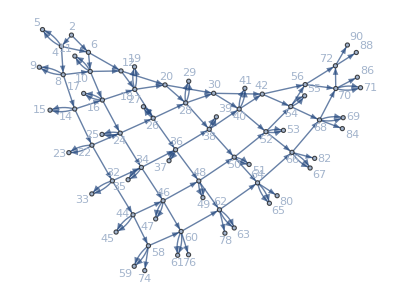

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
{{I-Cat, {, □, □, □, □, □, □, □, □, □, □, □, □, ], }}, {reps(len), , (), , , , , , , , , , , , , }, {, , , (), (), , , , , , ( ), , , ( ), ↖, }, {, , , , , ()(), , , (), ↖, , ( ), ↖, , , }, {, , , , , , (), ↖, , , , , , , , }}
```

```mathematica
{$debug=True,RepsLen[IC2D4],$debug=False}[[2]]
```

{}: {1,1}

{1,1,2,2 k}: {1,1}

€^(-1+k)[{},{1,1,2,2 k}]: {-1+k,2}

{}: {1,1}

{2 k,2 (1+k)}: {1,1}

€_(k⊨1)^8[€^(-1+k)[{},{1,1,2,2 k}],{},{2 k,2 (1+k)}]: {8,2+2 (-1+k)}

{{8,2+2 (-1+k)}}

```mathematica
IC2D4a={IndexedConcatenate[IndexedConcatenate[{},{1,1,2,2k},{j,1,k-1}],{},{2k,2(1+k)},{k,1,8}]}
```

{€_(k⊨1)^8[€_(j⊨1)^(-1+k)[{},{1,1,2,2 k}],{},{2 k,2 (1+k)}]}

### Figure 6e

```mathematica
IC2c={IndexedConcatenate[IndexedConcatenate[{k,k+1},k],{k,1,9}]}
```

{€_(k⊨1)^9[€^k[{k,1+k}]]}

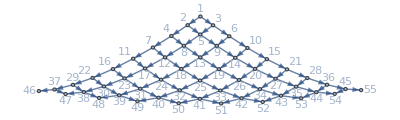

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
{{I-Cat, {, □, □, □, □, □, □, □, □, □, □, □, □, ], }}, {reps(len), , (), , , , , , , , , , , , , }, {, , , (), (), , , , , , ( ), , , ( ), ↖, }, {, , , , , ()(), , , (), ↖, , ( ), ↖, , , }, {, , , , , , (), ↖, , , , , , , , }}
```

```mathematica
{$debug=True,RepsLen[IC2c],$debug=False}[[2]]
```

{k,1+k}: {1,1}

€^k[{k,1+k}]: {k,1}

€_(k⊨1)^9[€^k[{k,1+k}]]: {9,k}

{{9,k}}

### Figure 6f

```mathematica
IC2j={IndexedConcatenate[{-1 + 2^k, 2^k, 1 + 2^k}, IndexedConcatenate[{1 + 2^k}, 1 + 2^k], {1}, 
 IndexedConcatenate[{1, -1 + 2^k + j, 2^k + j}, {j, 1, -1 + 2^k}], {k, 1, 10}]}
```

{€_(k⊨1)^10[{-1+2^k,2^k,1+2^k},€^(1+2^k)[{1+2^k}],{1},€_(j⊨1)^(-1+2^k)[{1,-1+2^k+j,2^k+j}]]}

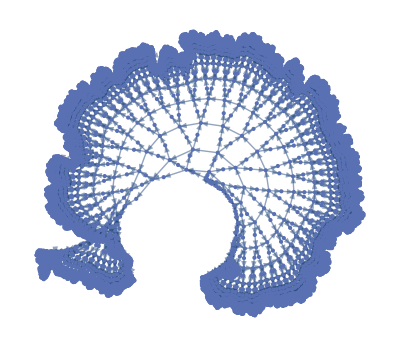

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->None,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
{{I-Cat, {, □, □, □, □, □, □, □, □, □, □, □, □, ], }}, {reps(len), , (), , , , , , , , , , , , , }, {, , , (), (), , , , , , ( ), , , ( ), ↖, }, {, , , , , ()(), , , (), ↖, , ( ), ↖, , , }, {, , , , , , (), ↖, , , , , , , , }}
```

```mathematica
{$debug=True,RepsLen[IC2j],$debug=False}[[2]]
```

{-1+2^k,2^k,1+2^k}: {1,1}

{1+2^k}: {1,1}

€^(1+2^k)[{1+2^k}]: {1+2^k,1}

{1}: {1,1}

{1,-1+2^k+j,2^k+j}: {1,1}

€_(j⊨1)^(-1+2^k)[{1,-1+2^k+j,2^k+j}]: {-1+2^k,1}

€_(k⊨1)^10[{-1+2^k,2^k,1+2^k},€^(1+2^k)[{1+2^k}],{1},€_(j⊨1)^(-1+2^k)[{1,-1+2^k+j,2^k+j}]]: {10,2+2^(1+k)}

{{10,2+2^(1+k)}}

## Trying again

### Example 1

```mathematica
{{I-Cat, reps, len, reps, len}, {{€^7[{1,6,8},{},{€^4[2]},€^2[{1,€^3[3]},{}]]}, 1, 1, 1, 1}, {{€^7[{1,6,8},{},{€^4[2]},€^2[{1,€^3[3]},{}]]}, , , 2, 2}, {{€^7[{1,6,8},{},{€^4[2]},€^2[{1,€^3[3]},{}]]}, , , 7, 7}, {{€^7[{1,6,8},{},{€^4[2]},€^2[{1,€^3[3]},{}]]}, , , 1, 49}}
```

```mathematica
{{I-Cat, {, €_(k⊨0)^6[, {1,6,8},, {},, {€^4[2]},, €_(j⊨0)^1[, {1,€^3[3]},, {}, ], ], }}, {raw v #, , , 1, 2, 3, , 4, 5, , , }, {v #, , , 7k+1, 7k+2, 7k+3, , 7k+2j+4, 7k+2j+5, , , }, {reps, , 7, 1, 1, 1, 2, 1, 1, , , }, {len, , 7, 1, 1, 1, 2, 1, 1, , , }}
```

This looks helpful. The lists (and ONLY the lists) each receive a raw vertex number: 1, 2, 3, 4, 5. To these are added 7k (for the lists inside the outer I-Cat) or 7k + 2j (for the lists inside the k- and the j- I-Cat.  The len & reps have to be found recursively, which pretty well requires all lists to have reps = 1 and len = 1, but then the vertex number is the (raw v #) + len * (I-Cat Index), with the additional term included for all I-Cats bracketing the given list. We will replace each list l by Rule[vertex number -> vertex number + #]& /@ l, to rebuild the edges of the graph inside the nested I-Cat object.

```mathematica
myICatObj={€^7[{1,6,8},{},{€^4[2]},€^2[{1,€^3[3]},{}]]};
```

```mathematica
Position[myICatObj,List]
```

{{0},{1,1,0},{1,2,0},{1,3,0},{1,4,1,0},{1,4,2,0}}

```mathematica
Most /@ Rest[Position[myICatObj,List]]
```

{{1,1},{1,2},{1,3},{1,4,1},{1,4,2}}

```mathematica
myICatObj[[1]]
```

€^7[{1,6,8},{},{€^4[2]},€^2[{1,€^3[3]},{}]]

```mathematica
myICatObj[[1,4]]
```

€^2[{1,€^3[3]},{}]

### Example 2

```mathematica
pentagraph={IndexedConcatenate[
{1,5n+4,5n+5},
IndexedConcatenate[
IndexedConcatenate[{1},{i,1,n}],
{1,5n+5+k},
{k,1,4}],
IndexedConcatenate[{1},{j,1,n-1}],
{},
{n,1,8}]};
Graph3D[FromNetDifferenceSets[ExpandAll[pentagraph]]]
```

-Graphics3D-

{€_(n⊨1)^8[{1,5 n+4,5 n+5},€_(k⊨1)^4[€_(i⊨1)^n[{1}],{1,k+5 n+5}],€_(j⊨1)^(n-1)[{1}],{}]}

```mathematica
{{I-Cat, {, €_(n⊨0)^7[, {1,5 n+4,5 n+5},, €_(k⊨0)^3[, €_(i⊨0)^(n-1)[, {1}, ],, {1,k+5 n+5}, ],, €_(j⊨0)^(n-2)[, {1}, ],, {}, ], }}, {raw v #, , , 1, , , 2, , 3, , , 4, , 5, , }, {raw v # 
T2, , , 1, , , 2, , 2+n, , , 2+4(n+1)
=4n+6, , (4n+6)+(n-1)
=5n+5, , }, {v #, , , (5n+5)n
+1, , , (5n+5)n
+(n+1)k
+1i
+2, , (5n+5)n
+(n+1)k
+1n
+3
 (or maybe 0|1?), , , (5n+5)n
+(n+1)4
+4
(or maybe 0|1?), , (5n+5)n
+(n+1)4
+1(n-1)
+5
(or maybe 0|1?), , }, {reps, , 8, 1, 4, n, 1, , 1, , n-1, 1, , 1, , }, {len, , 5n+5, 1, n+1, 1, 1, , 1, , 1, 1, , 1, , }, {reps×len, , 40(n+1), 1, 4(n+1), n, 1, , 1, , n-1, 1, , 1, , □}}
```

```mathematica
{$debug=True,RepsLen[pentagraph],$debug=False}[[2]]
```

{1,4+5 n,5+5 n}: {1,1}

{1}: {1,1}

€_(i⊨1)^n[{1}]: {n,1}

{1,5+k+5 n}: {1,1}

€_(k⊨1)^4[€_(i⊨1)^n[{1}],{1,5+k+5 n}]: {4,1+n}

{1}: {1,1}

€_(j⊨1)^(-1+n)[{1}]: {-1+n,1}

{}: {1,1}

€_(n⊨1)^8[{1,4+5 n,5+5 n},€_(k⊨1)^4[€_(i⊨1)^n[{1}],{1,5+k+5 n}],€_(j⊨1)^(-1+n)[{1}],{}]: {8,1+n+4 (1+n)}

{{8,1+n+4 (1+n)}}

I feel the need to add the terms in orange to any terms that follow a completed I-Cat, and then maybe the raw v # that follows needs to reset to 0 or 1. I can’t quite work it out without trying cases: n=0, k=0, but we’ve had all n of the len 1 entries in the innermost I-Cat, so that vertex shouldn’t be +3, it should be  + 1 + 1n + 1 (still with the (5n+5)n+(n+1)k in front of that. I think the reason this didn’t show up in the first example is that no I-Cats completed until after the last list, but here we complete two different I-Cats and go on. The +3 was assuming 2 completed lists of len 1 each, but actually we had n+1. Does thing give a rule for continuing?

```mathematica
Most /@ Rest[Position[prepIC[pentagraph],List]]
```

{{1,1},{1,2,1,1},{1,2,2},{1,3,1},{1,4}}

```mathematica
pentagraph
```

{€_(n⊨1)^8[{1,5 n+4,5 n+5},€_(k⊨1)^4[€_(i⊨1)^n[{1}],{1,k+5 n+5}],€_(j⊨1)^(n-1)[{1}],{}]}

```mathematica
pentagraph[[1]]
```

€_(n⊨1)^8[{1,5 n+4,5 n+5},€_(k⊨1)^4[€_(i⊨1)^n[{1}],{1,k+5 n+5}],€_(j⊨1)^(n-1)[{1}],{}]

```mathematica
pentagraph[[1,2]]
```

€_(k⊨1)^4[€_(i⊨1)^n[{1}],{1,k+5 n+5}]

```mathematica
pentagraph[[1,2,1]]
```

€_(i⊨1)^n[{1}]

```mathematica
pentagraph[[1,3]]
```

€_(j⊨1)^(n-1)[{1}]

```mathematica
pentagraph
```

{€_(n⊨1)^8[{1,5 n+4,5 n+5},€_(k⊨1)^4[€_(i⊨1)^n[{1}],{1,k+5 n+5}],€_(j⊨1)^(n-1)[{1}],{}]}

```mathematica
{{I-Cat, {, €_(n⊨1)^8[, {1,5 n+4,5 n+5},, €_(k⊨1)^4[, €_(i⊨1)^n[, {1}, ],, {1,k+5 n+5}, ],, €_(j⊨1)^(n-1)[, {1}, ],, {}, ], }}, {Position, , , 1, , , 1, , 1, , , 1, , 1, , }, {, , , 1, , , 2, , 2, , , 3, , 4, , }, {, , , , , , 1, , 2, , , 1, , , , }, {, , , , , , 1, , , , , , , , , }, {raw v # 
T3, , , 1, , , 1+1
=2, , 2+n
=n+2, , , 2+4(n+1)
=4n+6, , (4n+6)+(n-1)
=5n+5, , }, {v #, , , (5n+5)(n-1)
+1, , , (5n+5)(n-1)
+(n+1)(k-1)
+1(i-1)
+2, , (5n+5)(n-1)
+(n+1)(k-1)
+1n
+2, , , (5n+5)(n-1)
+(n+1)4
+(n-1)(j-1)
+2, , (5n+5)(n-1)
+(n+1)4+(n-1)1

+2, , }, {reps, , 8, 1, 4, n, 1, , 1, , n-1, 1, , 1, , }, {len, , 5n+5, 1, n+1, 1, 1, , 1, , 1, 1, , 1, , }, {reps×len, , 40(n+1), 1, 4(n+1), n, 1, , 1, , n-1, 1, , 1, , }}
```

This must be checked with small values of n, k, i.

```mathematica
{(5n+5)(n-1)+1,(5n+5)(n-1)+(n+1)(k-1)+1(i-1)+2,
(5n+5)(n-1)+(n+1)(k-1)+1n+2,
(5n+5)(n-1)+(n+1)4+(n-1)(j-1)+2,
(5n+5)(n-1)+(n+1)4+1(n-1)+2}/.n->1/.k->4/.i->1/.j->1
```

{1,8,9,10,10}

Need more examples.

```mathematica
pentagraph
```

{€_(n⊨1)^8[{1,5 n+4,5 n+5},€_(k⊨1)^4[€_(i⊨1)^n[{1}],{1,k+5 n+5}],€_(j⊨1)^(n-1)[{1}],{}]}

```mathematica
pentagraph//InputForm
```

```mathematica
{IndexedConcatenate[{1, 4 + 5*n, 5 + 5*n}, 
  IndexedConcatenate[IndexedConcatenate[{1}, {i, 0, n-1}], 
   {1, 6 + k + 5*n}, {k, 0, 3}], IndexedConcatenate[{1}, 
   {j, 0, -2 + n}], {}, {n, 1, 8}]}
```

{€_(n⊨1)^8[{1,5 n+4,5 n+5},€_(k⊨0)^3[€_(i⊨0)^(n-1)[{1}],{1,k+5 n+6}],€_(j⊨0)^(n-2)[{1}],{}]}

```mathematica
{IndexedConcatenate[{1, 9 + 5*n, 10 + 5*n}, 
  IndexedConcatenate[IndexedConcatenate[{1}, {i, 0, n}], 
   {1, 11 + k + 5*n}, {k, 0, 3}], IndexedConcatenate[{1}, 
   {j, 0, -1 + n}], {}, {n, 0, 7}]}
```

{€_(n⊨0)^7[{1,5 n+9,5 n+10},€_(k⊨0)^3[€_(i⊨0)^n[{1}],{1,k+5 n+11}],€_(j⊨0)^(n-1)[{1}],{}]}

```mathematica
ExpandAll[%183]==ExpandAll[pentagraph]
```

True

## Improved format for noting reps & len

Record reps & len in the format: reps(len)

For all lists in curly braces, reps(len) = 1(1).
For I-Cats use the iterator to calculate reps. (For iterator = {var,start,stop} or “var=start ... stop”, reps = stop - start + 1.) Temporarily leave len blank: reps( )

Everything inside an I-Cat is recorded one line down from the I-Cat itself. At the final closing bracket, add up all reps(len) entries since the beginning of the I-Cat, and put this sum in as the len.

In this example, color coding has been added to show which entries were added, and the sum (the len of the I-Cat) found:

```mathematica
{{I-Cat, {, €_(n⊨0)^7[, {1,5 n+9,5 n+10},, €_(k⊨0)^3[, €_(i⊨0)^n[, {1}, ],, {1,k+5 n+11}, ],, €_(j⊨0)^(n-1)[, {1}, ],, {}, ], }}, {reps(len), , 8(5(n+2)), , , , , , , , , , , , , }, {, , , 1(1), 4(n+2), , , , , , n(1), , , 1(1), ↖, }, {, , , , , (n+1)(1), , , 1(1), ↖, , 1(1), ↖, , , }, {, , , , , , 1(1), ↖, , , , , , , , }}
```

```mathematica
RepsLen[pentagraph]
```

{1,4+5 n,5+5 n}: {1,1}

{1}: {1,1}

€_(i⊨1)^n[{1}]: {n,1}

{1,5+k+5 n}: {1,1}

€_(k⊨1)^4[€_(i⊨1)^n[{1}],{1,5+k+5 n}]: {4,1+n}

{1}: {1,1}

€_(j⊨1)^(-1+n)[{1}]: {-1+n,1}

{}: {1,1}

€_(n⊨1)^8[{1,4+5 n,5+5 n},€_(k⊨1)^4[€_(i⊨1)^n[{1}],{1,5+k+5 n}],€_(j⊨1)^(-1+n)[{1}],{}]: {8,1+n+4 (1+n)}

{{8,1+n+4 (1+n)}}

Adding in rows with the Position of Lists information, and calculated raw vertex numbers and (complete) vertex numbers:

```mathematica
{{I-Cat, {, €_(n⊨0)^7[, {1,5 n+9,5 n+10},, €_(k⊨0)^3[, €_(i⊨0)^n[, {1}, ],, {1,k+5 n+11}, ],, €_(j⊨0)^(n-1)[, {1}, ],, {}, ], }}, {Position, , , 1, , , 1, , 1, , , 1, , 1, , }, {, , , 1, , , 2, , 2, , , 3, , 4, , }, {, , , , , , 1, , 2, , , 1, , , , }, {, , , , , , 1, , , , , , , , , }, {raw v # 
T3, , , 1, , , 1+1
=2, , 2+(n+1)
=n+3, , , 2+4(n+2)
=4n+4, , (4n+4)+(n)
=5n+4, , }, {v #, , , n(5(n+2))
+(1), , , n(5(n+2))
+k(n+2)
+i(1)
+(2), , n(5(n+2))
+k(n+2)
+(n+1)(1)
+(n+3), , , n(5(n+2))
+4(n+2)
+j(1)
+(4n+4), , n(5(n+2))
+n(n+2)
+n(1)
+(5n+4), , }, {reps(len), , 8(5(n+2)), , , , , , , , , , , , , }, {, , , 1(1), 4(n+2), , , , , , n(1), , , 1(1), ↖, }, {, , , , , (n+1)(1), , , 1(1), ↖, , 1(1), ↖, , , }, {, , , , , , 1(1), ↖, , , , , , , , }}
```

Whenever inside an I-Cat, there is a “var(len)” term added. After we exit from an I-Cat but remain on the same level, add “reps(len)” for the I-Cat. The latter are the entries shown in orange in the v # row.